```mathematica
<<NDSolve`FEM`
```

```mathematica
ToElementMesh[ImplicitRegion[x^2+y^2≤9,{x,y}]]
```

ElementMesh[{{-3.,3.},{-3.,3.}},{TriangleElement[<492>]}]

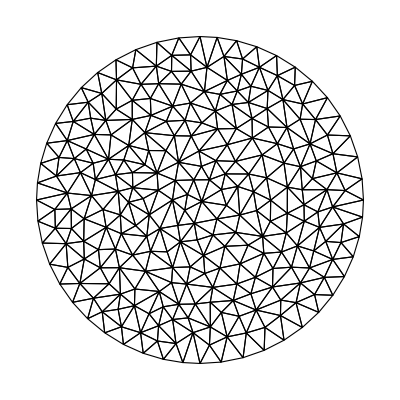

```mathematica
ToElementMesh[ImplicitRegion[x^2+y^2≤9,{x,y}]]["Wireframe"]
```

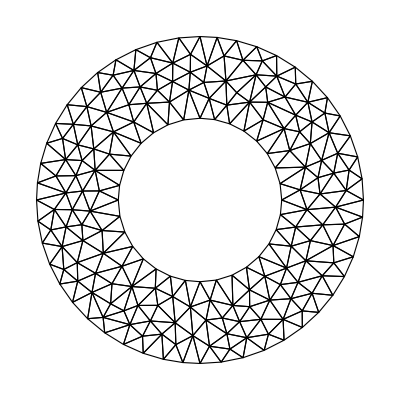

```mathematica
ToElementMesh[ImplicitRegion[1≤x^2+y^2≤4,{x,y}]]["Wireframe"]
```

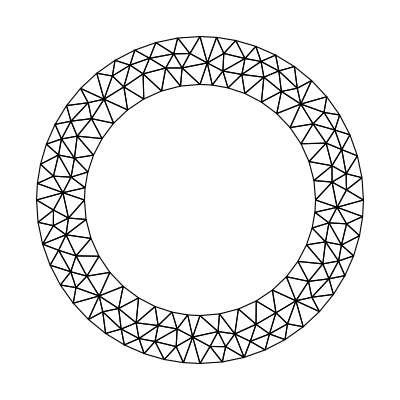

```mathematica
ToElementMesh[ImplicitRegion[1≤x^2+y^2≤2,{x,y}]]["Wireframe"]
```

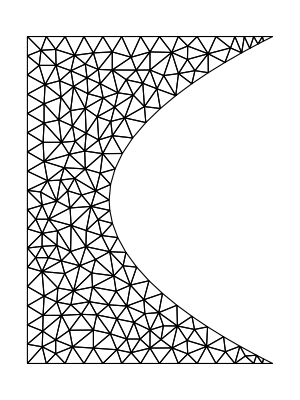

```mathematica
ToElementMesh[ImplicitRegion[x<y^2,{x,y}],{{-1/2,1},{-1,1}}]["Wireframe"]
```

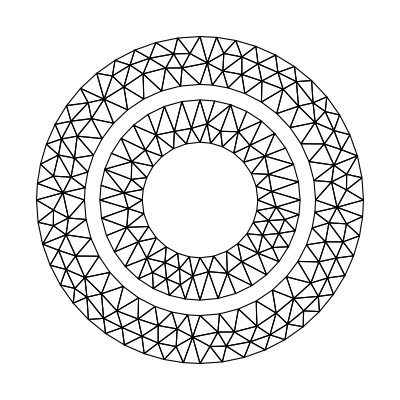

```mathematica
ToElementMesh[ImplicitRegion[(1≤x^2+y^2≤2)||(0.25≤x^2+y^2≤0.75),{x,y}]]["Wireframe"]
```

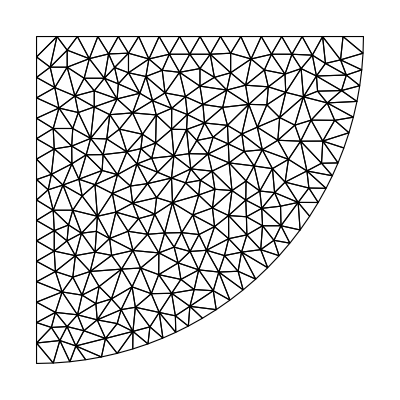

```mathematica
Block[
{x,y,r0=2,a=10},
ToElementMesh[
ImplicitRegion[(0≤(x-2a+r0)^2+(y-r0)^2≤r0^2&&(2a-r0)≤x≤2a&&0≤y≤r0),{x,y}]
]["Wireframe"]
]
```

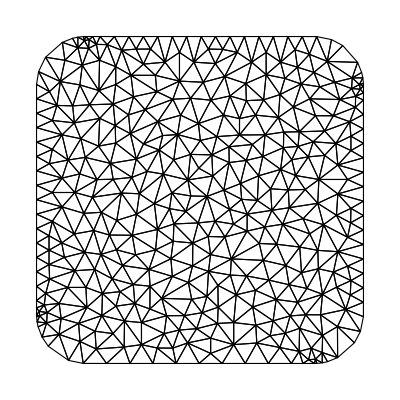

```mathematica
(* .... Setting up the finite element mesh for the conveyor belt geometry .... *)
Block[
{x,y,r0=3,a=10},
ToElementMesh[
ImplicitRegion[
(0≤(x-r0)^2+(y-r0)^2≤r0^2&&0≤x≤r0&&0≤y≤r0)||
(0≤(x-2a+r0)^2+(y-r0)^2≤r0^2&&(2a-r0)≤x≤2a&&0≤y≤r0)||
(0≤(x-2a+r0)^2+(y-2a+r0)^2≤r0^2&&(2a-r0)≤x≤2a&&(2a-r0)≤y≤2a)||
(0≤(x-r0)^2+(y-2a+r0)^2≤r0^2&&0≤x≤r0&&2a-r0≤y≤2a)||
(r0≤x≤2a-r0&&0≤y≤r0)||(2a-r0≤x≤2a&&r0≤y≤2a-r0)||
(r0≤x≤2a-r0&&2a-r0≤y≤2a)||(0≤x≤r0&&r0≤y≤2a-r0)||
(r0≤x≤2a-r0&&r0≤y≤2a-r0)
,{x,y}]
]["Wireframe"]
]
```

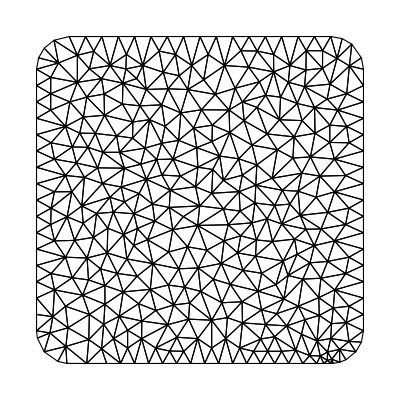

```mathematica
(* .... Setting up the finite element mesh for the conveyor belt geometry .... *)
Block[
{x,y,r0=2,a=10},
ToElementMesh[
ImplicitRegion[
(0≤(x-r0)^2+(y-r0)^2≤r0^2&&0≤x≤r0&&0≤y≤r0)||
(0≤(x-2a+r0)^2+(y-r0)^2≤r0^2&&(2a-r0)≤x≤2a&&0≤y≤r0)||
(0≤(x-2a+r0)^2+(y-2a+r0)^2≤r0^2&&(2a-r0)≤x≤2a&&(2a-r0)≤y≤2a)||
(0≤(x-r0)^2+(y-2a+r0)^2≤r0^2&&0≤x≤r0&&2a-r0≤y≤2a)||
(r0≤x≤2a-r0&&0≤y≤r0)||(2a-r0≤x≤2a&&r0≤y≤2a-r0)||
(r0≤x≤2a-r0&&2a-r0≤y≤2a)||(0≤x≤r0&&r0≤y≤2a-r0)||
(r0≤x≤2a-r0&&r0≤y≤2a-r0)
,{x,y}]
]["Wireframe"]
]
```

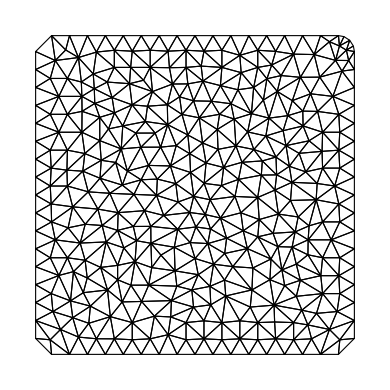

```mathematica
(* .... Setting up the finite element mesh for the conveyor belt geometry .... *)
Block[
{x,y,r0=1,a=10},
ToElementMesh[
ImplicitRegion[
(0≤(x-r0)^2+(y-r0)^2≤r0^2&&0≤x≤r0&&0≤y≤r0)||
(0≤(x-2a+r0)^2+(y-r0)^2≤r0^2&&(2a-r0)≤x≤2a&&0≤y≤r0)||
(0≤(x-2a+r0)^2+(y-2a+r0)^2≤r0^2&&(2a-r0)≤x≤2a&&(2a-r0)≤y≤2a)||
(0≤(x-r0)^2+(y-2a+r0)^2≤r0^2&&0≤x≤r0&&2a-r0≤y≤2a)||
(r0≤x≤2a-r0&&0≤y≤r0)||(2a-r0≤x≤2a&&r0≤y≤2a-r0)||
(r0≤x≤2a-r0&&2a-r0≤y≤2a)||(0≤x≤r0&&r0≤y≤2a-r0)||
(r0≤x≤2a-r0&&r0≤y≤2a-r0)
,{x,y}]
]["Wireframe"]
]
```

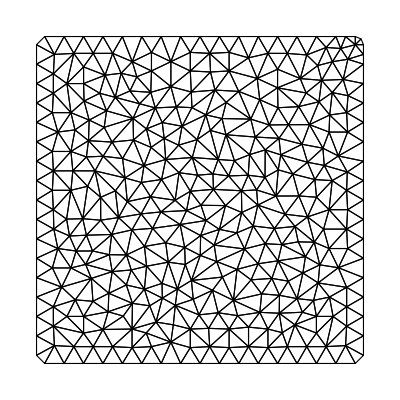

```mathematica
(* .... Setting up the finite element mesh for the conveyor belt geometry .... *)
Block[
{x,y,r0=0.5,a=10},
ToElementMesh[
ImplicitRegion[
(0≤(x-r0)^2+(y-r0)^2≤r0^2&&0≤x≤r0&&0≤y≤r0)||
(0≤(x-2a+r0)^2+(y-r0)^2≤r0^2&&(2a-r0)≤x≤2a&&0≤y≤r0)||
(0≤(x-2a+r0)^2+(y-2a+r0)^2≤r0^2&&(2a-r0)≤x≤2a&&(2a-r0)≤y≤2a)||
(0≤(x-r0)^2+(y-2a+r0)^2≤r0^2&&0≤x≤r0&&2a-r0≤y≤2a)||
(r0≤x≤2a-r0&&0≤y≤r0)||(2a-r0≤x≤2a&&r0≤y≤2a-r0)||
(r0≤x≤2a-r0&&2a-r0≤y≤2a)||(0≤x≤r0&&r0≤y≤2a-r0)||
(r0≤x≤2a-r0&&r0≤y≤2a-r0)
,{x,y}]
]["Wireframe"]
]
```

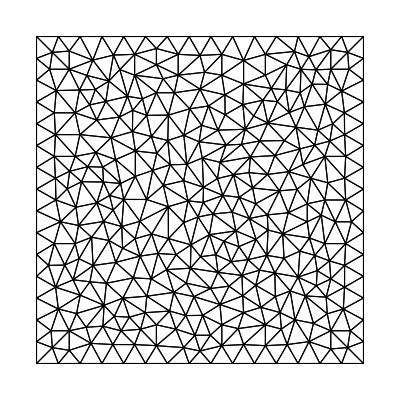

```mathematica
(* .... Setting up the finite element mesh for the conveyor belt geometry .... *)
Block[
{x,y,r0=0,a=10},
ToElementMesh[
ImplicitRegion[
(0≤(x-r0)^2+(y-r0)^2≤r0^2&&0≤x≤r0&&0≤y≤r0)||
(0≤(x-2a+r0)^2+(y-r0)^2≤r0^2&&(2a-r0)≤x≤2a&&0≤y≤r0)||
(0≤(x-2a+r0)^2+(y-2a+r0)^2≤r0^2&&(2a-r0)≤x≤2a&&(2a-r0)≤y≤2a)||
(0≤(x-r0)^2+(y-2a+r0)^2≤r0^2&&0≤x≤r0&&2a-r0≤y≤2a)||
(r0≤x≤2a-r0&&0≤y≤r0)||(2a-r0≤x≤2a&&r0≤y≤2a-r0)||
(r0≤x≤2a-r0&&2a-r0≤y≤2a)||(0≤x≤r0&&r0≤y≤2a-r0)||
(r0≤x≤2a-r0&&r0≤y≤2a-r0)
,{x,y}]
]["Wireframe"]
]
```

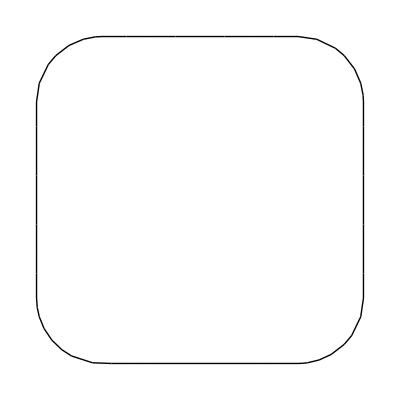

```mathematica
Block[
{x,y,r0=4,a=10},
ToBoundaryMesh[
ImplicitRegion[
(0≤(x-r0)^2+(y-r0)^2≤r0^2&&0≤x≤r0&&0≤y≤r0)||
(0≤(x-2a+r0)^2+(y-r0)^2≤r0^2&&(2a-r0)≤x≤2a&&0≤y≤r0)||
(0≤(x-2a+r0)^2+(y-2a+r0)^2≤r0^2&&(2a-r0)≤x≤2a&&(2a-r0)≤y≤2a)||
(0≤(x-r0)^2+(y-2a+r0)^2≤r0^2&&0≤x≤r0&&2a-r0≤y≤2a)||
(r0≤x≤2a-r0&&0≤y≤r0)||(2a-r0≤x≤2a&&r0≤y≤2a-r0)||
(r0≤x≤2a-r0&&2a-r0≤y≤2a)||(0≤x≤r0&&r0≤y≤2a-r0)||
(r0≤x≤2a-r0&&r0≤y≤2a-r0)
,{x,y}]
]["Wireframe"]
]
```

```mathematica
3.2*10^(-10)/(8.85*10^(-12))
```

36.1582

```mathematica
(* Now let us try solving the electrostatics problem in the conveyor belt region using ToElementMesh and NDSolve *)
```

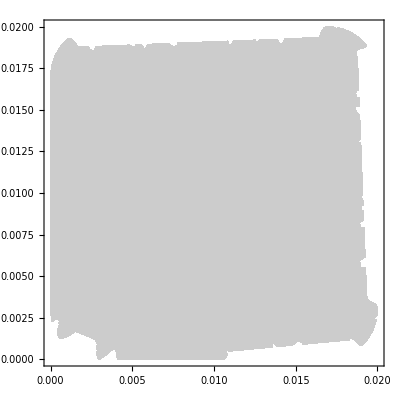

```mathematica
Block[
{x,y,a=10^(-2),r0=3*10^(-3),Ω,mesh,boundary,Q=3.2*10^(-10),ϵ0=8.85*10^(-12),ϕ,u},
Ω=ImplicitRegion[
(0≤(x-r0)^2+(y-r0)^2≤r0^2&&0≤x≤r0&&0≤y≤r0)||
(0≤(x-2a+r0)^2+(y-r0)^2≤r0^2&&(2a-r0)≤x≤2a&&0≤y≤r0)||
(0≤(x-2a+r0)^2+(y-2a+r0)^2≤r0^2&&(2a-r0)≤x≤2a&&(2a-r0)≤y≤2a)||
(0≤(x-r0)^2+(y-2a+r0)^2≤r0^2&&0≤x≤r0&&2a-r0≤y≤2a)||
(r0≤x≤2a-r0&&0≤y≤r0)||(2a-r0≤x≤2a&&r0≤y≤2a-r0)||
(r0≤x≤2a-r0&&2a-r0≤y≤2a)||(0≤x≤r0&&r0≤y≤2a-r0)||
(r0≤x≤2a-r0&&r0≤y≤2a-r0)
,{x,y}];
mesh=ToElementMesh[Ω];
boundary=ToBoundaryMesh[Ω];
ϕ=NDSolveValue[{D[u[x,y],{x,2}]+D[u[x,y],{y,2}]==-Q/ϵ0 DiracDelta[x-a]DiracDelta[y-a],DirichletCondition[u[x,y]==100,{x,y}∈boundary]},u,{x,y}∈mesh];
Show[
ContourPlot[ϕ[x,y],{x,y}∈ Ω],PlotRange->{{0,2a},{0,2a}}
]
]
```